```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/armin/my_programs/alphaLoopMisc/graph_generation/example

```mathematica
allGraphs=ToExpression["{"<>StringDrop[StringReplace[Import["ggHH.qgr"],{"**NewDiagram**"->",","\n"->""}]<>"}",1]];
```

```mathematica
ClearAll[plotGraph]
plotGraph[graph_,imSize_:Scaled[0.5]]:=Module[{},
Print[GraphComputation`GraphPlotLegacy[graph,Method->{"SpringElectricalEmbedding", "RepulsiveForcePower" -> -1.55},EdgeRenderingFunction->({{RGBColor[0.22,0.34,0.63],Arrowheads[0.015],Arrow[#]},If[#3=!=None,Text[#3,Mean[#1],Background->White],{}]}&),MultiedgeStyle->.3,SelfLoopStyle->All,ImageSize->imSize]]
]
```

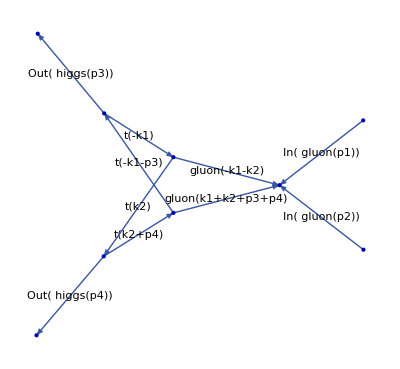

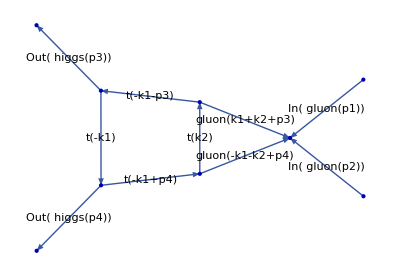

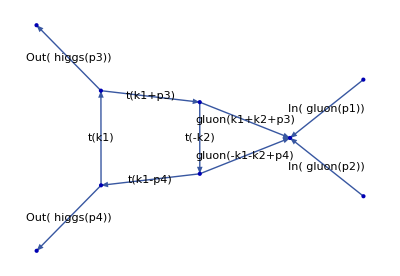

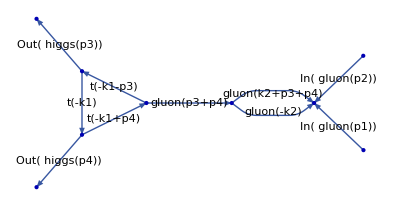

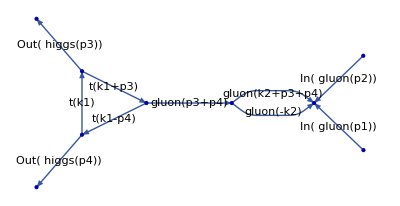

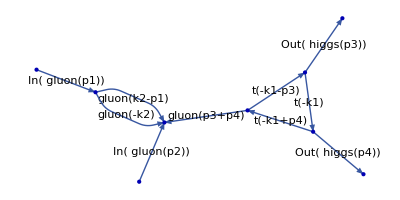

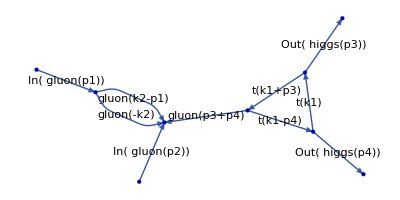

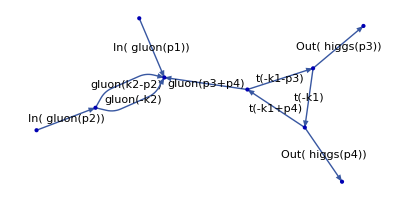

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
plotGraph[#,Scaled[.5]]&/@allGraphs[[All,2]]
```